```mathematica
$Assumptions={κ∈Reals,κ>0, g0>0,  g0∈Reals,ωp∈Reals,ω[x_]∈Reals,t∈Reals, τ∈Reals,μ∈Integers}
```

{κ∈ℝ,κ>0,g0>0,g0∈ℝ,ωp∈ℝ,ω[x_]∈ℝ,t∈ℝ,τ∈ℝ,μ∈ℤ}

```mathematica
validTriads[μ_]:=Select[Tuples[{1,2, 3},3],(#[[1]]-#[[2]]+#[[3]]==μ)&]
(*Do[Print["μ = ",μ," → ",validTriads[μ]],{μ,{1,2,3}}];*)
```

```mathematica
eq[μ_]:=D[A[μ][t],t]==-(κ/2) A[μ][t]+
Sqrt[κe] S Exp[-I (ωp-ω[μ]) t] KroneckerDelta[μ,2]-
I g0 Sum[With[{α=triad[[1]],β=triad[[2]],γ=triad[[3]]},
A[α][t]  Conjugate[A[β][t]] A[γ][t] Exp[-I (ω[α]-ω[β]+ω[γ]-ω[μ]) t]
],
{triad,validTriads[μ]}
];
eqsystem = Table[eq[μ],{μ,{1,2,3}}]
```

{A[1]'[t]==-1/2 κ A[1][t]-ⅈ g0 (Conjugate[A[1][t]] (A[1][t])^2+2 Conjugate[A[2][t]] A[1][t] A[2][t]+ⅇ^(-ⅈ t (-ω[1]+2 ω[2]-ω[3])) Conjugate[A[3][t]] (A[2][t])^2+2 Conjugate[A[3][t]] A[1][t] A[3][t]),A[2]'[t]==ⅇ^(-ⅈ t (ωp-ω[2])) S √κe-1/2 κ A[2][t]-ⅈ g0 (2 Conjugate[A[1][t]] A[1][t] A[2][t]+Conjugate[A[2][t]] (A[2][t])^2+2 ⅇ^(-ⅈ t (ω[1]-2 ω[2]+ω[3])) Conjugate[A[2][t]] A[1][t] A[3][t]+2 Conjugate[A[3][t]] A[2][t] A[3][t]),A[3]'[t]==-1/2 κ A[3][t]-ⅈ g0 (ⅇ^(-ⅈ t (-ω[1]+2 ω[2]-ω[3])) Conjugate[A[1][t]] (A[2][t])^2+2 Conjugate[A[1][t]] A[1][t] A[3][t]+2 Conjugate[A[2][t]] A[2][t] A[3][t]+Conjugate[A[3][t]] (A[3][t])^2)}

```mathematica
A[x_][t_]:=Sqrt[κ/(2 g0)] a[x][t] Exp[I (ω[x]-ωp) t]
expr = eqsystem//Simplify
```

{ⅈ (κ Conjugate[a[1][t]] (a[1][t])^2+κ Conjugate[a[3][t]] (a[2][t])^2+a[1][t] (-ⅈ κ-2 ωp+2 ω[1]+2 κ Conjugate[a[2][t]] a[2][t]+2 κ Conjugate[a[3][t]] a[3][t])-2 ⅈ a[1]'[t])==0,4 S √κe-ⅈ √2 κ √(κ/g0) Conjugate[a[2][t]] (a[2][t])^2-2 ⅈ √2 κ √(κ/g0) Conjugate[a[2][t]] a[1][t] a[3][t]-ⅈ √2 √(κ/g0) a[2][t] (-ⅈ κ-2 ωp+2 ω[2]+2 κ Conjugate[a[1][t]] a[1][t]+2 κ Conjugate[a[3][t]] a[3][t])==2 √2 √(κ/g0) a[2]'[t],ⅈ ((-ⅈ κ-2 ωp+2 ω[3]+2 κ Conjugate[a[2][t]] a[2][t]) a[3][t]+κ Conjugate[a[3][t]] (a[3][t])^2+κ Conjugate[a[1][t]] ((a[2][t])^2+2 a[1][t] a[3][t])-2 ⅈ a[3]'[t])==0}

```mathematica
expr = expr/. t->(2 τ)/κ
```

{ⅈ (κ Conjugate[a[1][(2 τ)/κ]] (a[1][(2 τ)/κ])^2+κ Conjugate[a[3][(2 τ)/κ]] (a[2][(2 τ)/κ])^2+a[1][(2 τ)/κ] (-ⅈ κ-2 ωp+2 ω[1]+2 κ Conjugate[a[2][(2 τ)/κ]] a[2][(2 τ)/κ]+2 κ Conjugate[a[3][(2 τ)/κ]] a[3][(2 τ)/κ])-2 ⅈ a[1]'[(2 τ)/κ])==0,4 S √κe-ⅈ √2 κ √(κ/g0) Conjugate[a[2][(2 τ)/κ]] (a[2][(2 τ)/κ])^2-2 ⅈ √2 κ √(κ/g0) Conjugate[a[2][(2 τ)/κ]] a[1][(2 τ)/κ] a[3][(2 τ)/κ]-ⅈ √2 √(κ/g0) a[2][(2 τ)/κ] (-ⅈ κ-2 ωp+2 ω[2]+2 κ Conjugate[a[1][(2 τ)/κ]] a[1][(2 τ)/κ]+2 κ Conjugate[a[3][(2 τ)/κ]] a[3][(2 τ)/κ])==2 √2 √(κ/g0) a[2]'[(2 τ)/κ],ⅈ ((-ⅈ κ-2 ωp+2 ω[3]+2 κ Conjugate[a[2][(2 τ)/κ]] a[2][(2 τ)/κ]) a[3][(2 τ)/κ]+κ Conjugate[a[3][(2 τ)/κ]] (a[3][(2 τ)/κ])^2+κ Conjugate[a[1][(2 τ)/κ]] ((a[2][(2 τ)/κ])^2+2 a[1][(2 τ)/κ] a[3][(2 τ)/κ])-2 ⅈ a[3]'[(2 τ)/κ])==0}

```mathematica
rulesTime={ a[n_][(2 τ)/κ]->a[n][τ],Derivative[1][a[n_]][(2 τ)/κ]->(κ/2) Derivative[1][a[n]][τ]};
expr= expr/.rulesTime//Simplify
```

{ⅈ (κ Conjugate[a[1][τ]] (a[1][τ])^2+κ Conjugate[a[3][τ]] (a[2][τ])^2+a[1][τ] (-ⅈ κ-2 ωp+2 ω[1]+2 κ Conjugate[a[2][τ]] a[2][τ]+2 κ Conjugate[a[3][τ]] a[3][τ])-ⅈ κ a[1]'[τ])==0,4 S √κe-ⅈ √2 κ √(κ/g0) Conjugate[a[2][τ]] (a[2][τ])^2-2 ⅈ √2 κ √(κ/g0) Conjugate[a[2][τ]] a[1][τ] a[3][τ]-ⅈ √2 √(κ/g0) a[2][τ] (-ⅈ κ-2 ωp+2 ω[2]+2 κ Conjugate[a[1][τ]] a[1][τ]+2 κ Conjugate[a[3][τ]] a[3][τ])==√2 κ √(κ/g0) a[2]'[τ],ⅈ ((-ⅈ κ-2 ωp+2 ω[3]+2 κ Conjugate[a[2][τ]] a[2][τ]) a[3][τ]+κ Conjugate[a[3][τ]] (a[3][τ])^2+κ Conjugate[a[1][τ]] ((a[2][τ])^2+2 a[1][τ] a[3][τ])-ⅈ κ a[3]'[τ])==0}

```mathematica
expr//MatrixForm
```

(ⅈ (κ Conjugate[a[1][τ]] (a[1][τ])^2+κ Conjugate[a[3][τ]] (a[2][τ])^2+a[1][τ] (-ⅈ κ-2 ωp+2 ω[1]+2 κ Conjugate[a[2][τ]] a[2][τ]+2 κ Conjugate[a[3][τ]] a[3][τ])-ⅈ κ a[1]'[τ])==0
4 S √κe-ⅈ √2 κ √(κ/g0) Conjugate[a[2][τ]] (a[2][τ])^2-2 ⅈ √2 κ √(κ/g0) Conjugate[a[2][τ]] a[1][τ] a[3][τ]-ⅈ √2 √(κ/g0) a[2][τ] (-ⅈ κ-2 ωp+2 ω[2]+2 κ Conjugate[a[1][τ]] a[1][τ]+2 κ Conjugate[a[3][τ]] a[3][τ])==√2 κ √(κ/g0) a[2]'[τ]
ⅈ ((-ⅈ κ-2 ωp+2 ω[3]+2 κ Conjugate[a[2][τ]] a[2][τ]) a[3][τ]+κ Conjugate[a[3][τ]] (a[3][τ])^2+κ Conjugate[a[1][τ]] ((a[2][τ])^2+2 a[1][τ] a[3][τ])-ⅈ κ a[3]'[τ])==0)

```mathematica
(*Isolando o termo da derivada*)
expr = Solve[expr,{Derivative[1][a[1]][τ],Derivative[1][a[2]][τ],Derivative[1][a[3]][τ]}][[1]]
```

{a[1]'[τ]→1/κ(-κ a[1][τ]+ⅈ (2 ωp a[1][τ]-2 ω[1] a[1][τ]-κ Conjugate[a[1][τ]] (a[1][τ])^2-2 κ Conjugate[a[2][τ]] a[1][τ] a[2][τ]-κ Conjugate[a[3][τ]] (a[2][τ])^2-2 κ Conjugate[a[3][τ]] a[1][τ] a[3][τ])),a[2]'[τ]→1/κ(-(√(g0/κ) (-4 S √κe+√2 κ √(κ/g0) a[2][τ]))/(√2)+ⅈ (2 ωp a[2][τ]-2 ω[2] a[2][τ]-2 κ Conjugate[a[1][τ]] a[1][τ] a[2][τ]-κ Conjugate[a[2][τ]] (a[2][τ])^2-2 κ Conjugate[a[2][τ]] a[1][τ] a[3][τ]-2 κ Conjugate[a[3][τ]] a[2][τ] a[3][τ])),a[3]'[τ]→1/κ(-κ a[3][τ]+ⅈ (-κ Conjugate[a[1][τ]] (a[2][τ])^2+2 ωp a[3][τ]-2 ω[3] a[3][τ]-2 κ Conjugate[a[1][τ]] a[1][τ] a[3][τ]-2 κ Conjugate[a[2][τ]] a[2][τ] a[3][τ]-κ Conjugate[a[3][τ]] (a[3][τ])^2))}

```mathematica
expr = expr/.S->s*κ/Sqrt[(8*κe*g0/κ)]//Simplify
```

{a[1]'[τ]→-1/κ ⅈ (κ Conjugate[a[1][τ]] (a[1][τ])^2+κ Conjugate[a[3][τ]] (a[2][τ])^2+a[1][τ] (-ⅈ κ-2 ωp+2 ω[1]+2 κ Conjugate[a[2][τ]] a[2][τ]+2 κ Conjugate[a[3][τ]] a[3][τ])),a[2]'[τ]→s-ⅈ Conjugate[a[2][τ]] (a[2][τ])^2-2 ⅈ Conjugate[a[2][τ]] a[1][τ] a[3][τ]-(ⅈ a[2][τ] (-ⅈ κ-2 ωp+2 ω[2]+2 κ Conjugate[a[1][τ]] a[1][τ]+2 κ Conjugate[a[3][τ]] a[3][τ]))/κ,a[3]'[τ]→-1/κ ⅈ (a[3][τ] (-ⅈ κ-2 ωp+2 ω[3]+2 κ Conjugate[a[2][τ]] a[2][τ]+κ Conjugate[a[3][τ]] a[3][τ])+κ Conjugate[a[1][τ]] ((a[2][τ])^2+2 a[1][τ] a[3][τ]))}

```mathematica
expr = expr/.{(-2ωp+2ω[i_])->(κ) Δ[i]}//Simplify
```

{a[1]'[τ]→-ⅈ (Conjugate[a[1][τ]] (a[1][τ])^2+Conjugate[a[3][τ]] (a[2][τ])^2+a[1][τ] (-ⅈ+Δ[1]+2 Conjugate[a[2][τ]] a[2][τ]+2 Conjugate[a[3][τ]] a[3][τ])),a[2]'[τ]→s-ⅈ Conjugate[a[2][τ]] (a[2][τ])^2-2 ⅈ Conjugate[a[2][τ]] a[1][τ] a[3][τ]-ⅈ a[2][τ] (-ⅈ+Δ[2]+2 Conjugate[a[1][τ]] a[1][τ]+2 Conjugate[a[3][τ]] a[3][τ]),a[3]'[τ]→-ⅈ (a[3][τ] (-ⅈ+Δ[3]+2 Conjugate[a[2][τ]] a[2][τ]+Conjugate[a[3][τ]] a[3][τ])+Conjugate[a[1][τ]] ((a[2][τ])^2+2 a[1][τ] a[3][τ]))}

```mathematica
rhs=expr[[All,2]]
```

{-ⅈ (Conjugate[a[1][τ]] (a[1][τ])^2+Conjugate[a[3][τ]] (a[2][τ])^2+a[1][τ] (-ⅈ+Δ[1]+2 Conjugate[a[2][τ]] a[2][τ]+2 Conjugate[a[3][τ]] a[3][τ])),s-ⅈ Conjugate[a[2][τ]] (a[2][τ])^2-2 ⅈ Conjugate[a[2][τ]] a[1][τ] a[3][τ]-ⅈ a[2][τ] (-ⅈ+Δ[2]+2 Conjugate[a[1][τ]] a[1][τ]+2 Conjugate[a[3][τ]] a[3][τ]),-ⅈ (a[3][τ] (-ⅈ+Δ[3]+2 Conjugate[a[2][τ]] a[2][τ]+Conjugate[a[3][τ]] a[3][τ])+Conjugate[a[1][τ]] ((a[2][τ])^2+2 a[1][τ] a[3][τ]))}

```mathematica
odes=Thread[{a[1]'[τ],a[2]'[τ],a[3]'[τ]}==rhs]
```

{a[1]'[τ]==-ⅈ (Conjugate[a[1][τ]] (a[1][τ])^2+Conjugate[a[3][τ]] (a[2][τ])^2+a[1][τ] (-ⅈ+Δ[1]+2 Conjugate[a[2][τ]] a[2][τ]+2 Conjugate[a[3][τ]] a[3][τ])),a[2]'[τ]==s-ⅈ Conjugate[a[2][τ]] (a[2][τ])^2-2 ⅈ Conjugate[a[2][τ]] a[1][τ] a[3][τ]-ⅈ a[2][τ] (-ⅈ+Δ[2]+2 Conjugate[a[1][τ]] a[1][τ]+2 Conjugate[a[3][τ]] a[3][τ]),a[3]'[τ]==-ⅈ (a[3][τ] (-ⅈ+Δ[3]+2 Conjugate[a[2][τ]] a[2][τ]+Conjugate[a[3][τ]] a[3][τ])+Conjugate[a[1][τ]] ((a[2][τ])^2+2 a[1][τ] a[3][τ]))}

```mathematica
params={s->2,Δ[1]->0,Δ[2]->0,Δ[3]->0};
ics={a[1][0]==0,a[2][0]==0.1,a[3][0]==0};
```

```mathematica
subs={a[1][τ]->x1[τ]+I y1[τ],a[2][τ]->x2[τ]+I y2[τ],a[3][τ]->x3[τ]+I y3[τ]};
subsC={Conjugate[a[1][τ]]->x1[τ]-I y1[τ],Conjugate[a[2][τ]]->x2[τ]-I y2[τ],Conjugate[a[3][τ]]->x3[τ]-I y3[τ]};
```

```mathematica
eqs = rhs/.subs/.params//ReIm//ComplexExpand//Simplify
```

{{-x1[τ]+x1[τ]^2 y1[τ]+2 x3[τ]^2 y1[τ]+y1[τ]^3+2 x2[τ] x3[τ] y2[τ]+2 y1[τ] y2[τ]^2+x2[τ]^2 (2 y1[τ]-y3[τ])+y2[τ]^2 y3[τ]+2 y1[τ] y3[τ]^2,-x1[τ]^3-x2[τ]^2 x3[τ]-y1[τ]+x3[τ] y2[τ]^2-2 x2[τ] y2[τ] y3[τ]-x1[τ] (2 x2[τ]^2+2 x3[τ]^2+y1[τ]^2+2 y2[τ]^2+2 y3[τ]^2)},{2+2 x1[τ]^2 y2[τ]+x2[τ]^2 y2[τ]-2 x1[τ] x3[τ] y2[τ]+2 x3[τ]^2 y2[τ]+2 y1[τ]^2 y2[τ]+y2[τ]^3+2 y1[τ] y2[τ] y3[τ]+2 y2[τ] y3[τ]^2+x2[τ] (-1+2 x3[τ] y1[τ]+2 x1[τ] y3[τ]),-2 x1[τ]^2 x2[τ]-x2[τ]^3-(1+2 x3[τ] y1[τ]) y2[τ]-2 x1[τ] (x2[τ] x3[τ]+y2[τ] y3[τ])-x2[τ] (2 x3[τ]^2+2 y1[τ]^2+y2[τ]^2-2 y1[τ] y3[τ]+2 y3[τ]^2)},{-x3[τ]+2 x1[τ] x2[τ] y2[τ]+y1[τ] y2[τ]^2-x2[τ]^2 (y1[τ]-2 y3[τ])+2 x1[τ]^2 y3[τ]+x3[τ]^2 y3[τ]+2 y1[τ]^2 y3[τ]+2 y2[τ]^2 y3[τ]+y3[τ]^3,-2 x1[τ]^2 x3[τ]-2 x2[τ]^2 x3[τ]-x3[τ]^3-2 x3[τ] y1[τ]^2-2 x2[τ] y1[τ] y2[τ]-2 x3[τ] y2[τ]^2+x1[τ] (-x2[τ]^2+y2[τ]^2)-y3[τ]-x3[τ] y3[τ]^2}}

```mathematica
system={x1'[τ]==eqs[[1,1]],y1'[τ]==eqs[[1,2]],x2'[τ]==eqs[[2,1]],y2'[τ]==eqs[[2,2]],x3'[τ]==eqs[[3,1]],y3'[τ]==eqs[[3,2]]};
```

```mathematica
sol=NDSolve[Join[system/. params,{x1[0]==0,y1[0]==0,x2[0]==0.1,y2[0]==0,x3[0]==0,y3[0]==0}],{x1,y1,x2,y2,x3,y3},{τ,0,50}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],x2→InterpolatingFunction[…],y2→InterpolatingFunction[…],x3→InterpolatingFunction[…],y3→InterpolatingFunction[…]}}

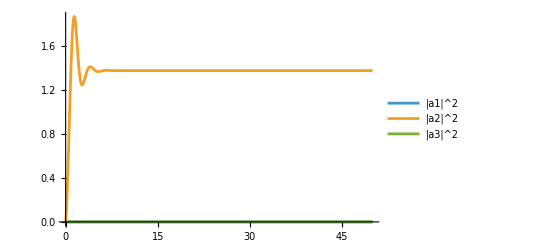

```mathematica
Plot[Evaluate[{x1[τ]^2+y1[τ]^2,x2[τ]^2+y2[τ]^2,x3[τ]^2+y3[τ]^2}/. sol],{τ,0,50},PlotLegends->{"|a1|^2","|a2|^2","|a3|^2"}]
```